## Plotting the

```mathematica
spin1={8.5,10.5,12.5,14.5,16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5,44.5,46.5,48.5};
spin2={13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5};
spin3={16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5};
spin4={23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5};
tsd1={0.1966,0.4597,0.7746,1.1609,1.6112,2.1265,2.7051,3.3441,4.0411,4.7937,5.5992,6.457,7.3667,8.3293,9.3458,10.4169,11.5431,12.7224,13.9491,15.2181,16.5221};
tsd2={1.3394,1.7467,2.2184,2.7527,3.3484,4.003,4.7143,5.4805,6.3004,7.1733,8.0998,9.08,10.1147,11.2036,12.3466,13.5441,14.7911};
tsd3={2.1237,2.6293,3.1973,3.8243,4.5094,5.2506,6.0465,6.8963,7.7988,8.7546,9.7638,10.8268,11.9392,13.0861};
tsd4={4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701};
thData={0.223918,0.504649,0.843114,1.23987,1.6953,2.20966,2.78313,3.41587,4.10797,4.85954,5.67062,6.54128,7.47154,8.46145,9.51102,10.6203,11.7892,13.0178,14.306,15.6539,17.0614,1.30802,1.73218,2.21124,2.746,3.33703,3.98475,4.6895,5.45152,6.27101,7.14813,8.08299,9.07568,10.1263,11.2347,12.4012,13.6255,14.9077,2.22448,2.72718,3.28235,3.89093,4.55364,5.27102,6.0435,6.87141,7.75499,8.69445,9.68991,10.7415,11.8492,13.0132,3.75449,4.47632,5.25763,6.0985,6.99896,7.95904,8.97878,10.0582,11.1973,12.396};
tsd1th=Table[thData[[i]],{i,1,21}];
tsd2th=Table[thData[[i]],{i,22,38}];
tsd3th=Table[thData[[i]],{i,39,52}];
tsd4th=Table[thData[[i]],{i,53,62}];
expData=Join[tsd1,tsd2,tsd3,tsd4];
n1=21;
n2=17;
n3=14;
n4=10;
data1exp=Table[{spin1[[i]],tsd1[[i]]},{i,1,Length[tsd1]}];
data2exp=Table[{spin2[[i]],tsd2[[i]]},{i,1,Length[tsd2]}];
data3exp=Table[{spin3[[i]],tsd3[[i]]},{i,1,Length[tsd3]}];
data4exp=Table[{spin4[[i]],tsd4[[i]]},{i,1,Length[tsd4]}];
data1th=Table[{spin1[[i]],tsd1th[[i]]},{i,1,Length[tsd1th]}];
data2th=Table[{spin2[[i]],tsd2th[[i]]},{i,1,Length[tsd2th]}];
data3th=Table[{spin3[[i]],tsd3th[[i]]},{i,1,Length[tsd3th]}];
data4th=Table[{spin4[[i]],tsd4th[[i]]},{i,1,Length[tsd4th]}];
SPINS=Join[spin1,spin2,spin3,spin4];
```

```mathematica
RMS[exp_,th_]:=Sqrt[Sum[(exp[[i]]-th[[i]])^2,{i,1,Length[exp]}]/(Length[exp]+1)];
```

```mathematica
RMS[expData,thData]
```

0.238279

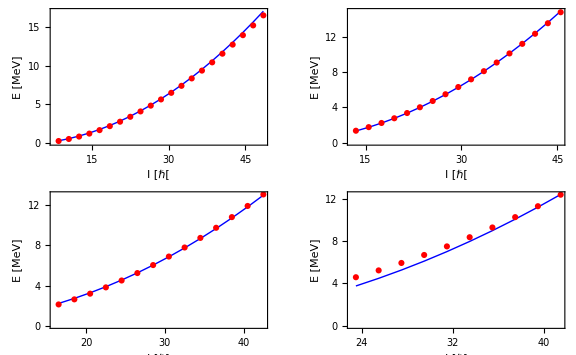

```mathematica
p1[exp_,th_]:=ListPlot[{exp,th},Frame->True,Axes->False,Joined->{False,True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic,None},FrameLabel->{"I [ℏ[","E [MeV]"},LabelStyle->{14,Bold,Black,FontFamily->"Times New Roman"}];
GraphicsGrid[{{p1[data1exp,data1th],p1[data2exp,data2th]}, 
 {p1[data3exp,data3th],p1[data4exp,data4th]}},Frame->None,ImageSize->Large]
```